```mathematica
Clear["Global`*"]
ig= Sqrt[(1-x^2)(x^2 + g * x + f)]/(x - a)
```

(√((1-x^2) (f+g x+x^2)))/(-a+x)

```mathematica
c=Sqrt[a*a-b*b]
```

√(a^2-b^2)

```mathematica
dm = b * z - a * Sqrt[c^2+z^2] / c^2
dp = b * z + a * Sqrt[c^2+z^2] / c^2
```

b z-(a √(a^2-b^2+z^2))/(a^2-b^2)

b z+(a √(a^2-b^2+z^2))/(a^2-b^2)

```mathematica
(a / (3 * c^2)) * (b + t * z) / ((t - dm)(t - dp)Sqrt[1-t^2])//FullSimplify
```

(a (a-z) (a+z) (b+t z))/(3 √(1-t^2) (a^2 (-1+t-b z)+z^2 (-t+b z)) (a^2 (1+t-b z)+z^2 (-t+b z)))

```mathematica
Integrate[(a / (3 * c^2)) * (b + t * z) / ((t - dm)(t - dp)Sqrt[1-t^2]),t]//FullSimplify
```

1/(3 a √z)(((b z^2 (1+z^2)-a^2 (b-z+b z^2)) ArcTan[(t √z √((z^2-b z^3+a^2 (-2+b z)) (a^2 b-z (1+b z))))/(z^2 (t+b (-1+√(1-t^2)) z)+a^2 (-t-(-1+√(1-t^2)) (-1+b z)))])/(√((z^2-b z^3+a^2 (-2+b z)) (a^2 b-z (1+b z))))+((-b z^2 (1+z^2)+a^2 (b+z+b z^2)) ArcTan[(t √z √((z+b (a-z) (a+z)) (-z^2 (1+b z)+a^2 (2+b z))))/(z^2 (t+b (-1+√(1-t^2)) z)-a^2 (t+(-1+√(1-t^2)) (1+b z)))])/(√((z+b (a-z) (a+z)) (-z^2 (1+b z)+a^2 (2+b z)))))

```mathematica
ArcTan[(t √z √((z^2-b z^3+a^2 (-2+b z)) (a^2 b-z (1+b z))))/(z^2 (t+b (-1+√(1-t^2)) z)+a^2 (-t-(-1+√(1-t^2)) (-1+b z)))]/.a->0.1/.b->0.05/.z->0.2/.t->-0.2
```

0.+1.51448 ⅈ

```mathematica
√((z^2-b z^3+a^2 (-2+b z)) (a^2 b-z (1+b z)))/.a->0.1/.b->0.05/.z->0.2/.t->-0.2
```

0.+0.0630044 ⅈ

```mathematica
1/(6 √(a^2) (a-z) (a+z))((a √(a^2) z-b (a-z) (a+z) (1+z^2)) Log[-a √(a^2)+z^2 (t-b z)+a^2 (-t+b z)]+(a √(a^2) z+b (a-z) (a+z) (1+z^2)) Log[a √(a^2)+z^2 (t-b z)+a^2 (-t+b z)])/.a->0.1/.b->0.05/.z->0.2/.t->-0.2
```

0.951045-0.621337 ⅈ

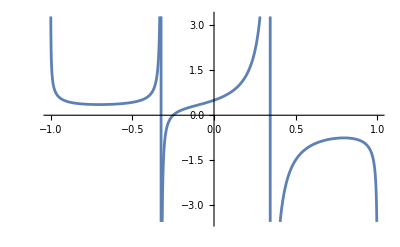

```mathematica
Plot[(a / (3 * c^2)) * (b + t * z) / ((t - dm)(t - dp)Sqrt[1-t^2])/.a->0.1/.b->0.05/.z->0.2,{t,-1,1}]
```

```mathematica
dp/.a->0.1/.b->0.05/.z->0.2
```

-0.323333

```mathematica
NIntegrate[(a / (3 * c^2)) * (b + t * z) / ((t - dm)(t - dp))/.a->0.1/.b->0.05/.z->0.2,{t,-0.2, 0.5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.34413}. NIntegrate obtained 0.498067 and 0.69449 for the integral and error estimates.

0.498067

```mathematica
ArcTan[I x]
```

ⅈ ArcTanh[x]

```mathematica
ArcTan[(t √z √((z^2-b z^3+a^2 (-2+b z)) (a^2 b-z (1+b z))))/(z^2 (t+b (-1+√(1-t^2)) z)+a^2 (-t-(-1+√(1-t^2)) (-1+b z)))]/√((z^2-b z^3+a^2 (-2+b z)) (a^2 b-z (1+b z)))/.a->0.1/.b->0.05/.z->0.2/.t->-0.2
```

24.0376+0. ⅈ

```mathematica
ArcTanh[(t √z √(-(z^2-b z^3+a^2 (-2+b z)) (a^2 b-z (1+b z))))/(z^2 (t+b (-1+√(1-t^2)) z)+a^2 (-t-(-1+√(1-t^2)) (-1+b z)))]/√(-(z^2-b z^3+a^2 (-2+b z)) (a^2 b-z (1+b z)))/.a->0.1/.b->0.05/.z->0.2/.t->0.5
```

32.3844-24.9315 ⅈ

```mathematica
1/(3 a √z)(((b z^2 (1+z^2)-a^2 (b-z+b z^2)) ArcTan[(t √z √((z^2-b z^3+a^2 (-2+b z)) (a^2 b-z (1+b z))))/(z^2 (t+b (-1+√(1-t^2)) z)+a^2 (-t-(-1+√(1-t^2)) (-1+b z)))])/(√((z^2-b z^3+a^2 (-2+b z)) (a^2 b-z (1+b z))))+((-b z^2 (1+z^2)+a^2 (b+z+b z^2)) ArcTan[(t √z √((z+b (a-z) (a+z)) (-z^2 (1+b z)+a^2 (2+b z))))/(z^2 (t+b (-1+√(1-t^2)) z)-a^2 (t+(-1+√(1-t^2)) (1+b z)))])/(√((z+b (a-z) (a+z)) (-z^2 (1+b z)+a^2 (2+b z)))))/.a->0.1/.b->0.05/.z->0.2/.t->0.5
```

0.92836-0.66155 ⅈ

```mathematica
ArcSin[1.0]
```

1.5708